```mathematica
h
```

h

```mathematica
Needs["ErrorBarPlots`"]
```

## Zeiten

Messungen der Periodendauer am Oszilloskop (1 s/div)
1. Wert mit keinem Zusatzgewicht , 2. mit 1 Zusatzgewicht, 3. mit 2 Zusatzgewichten

```mathematica
T={3.2,3.8,4.4}(*Periodendauer ungedämpft*)
Te={0.2,0.2,0.2}(*Fehler Periodendauer ungedämpft*)
```

{3.2,3.8,4.4}

{0.2,0.2,0.2}

```mathematica
Tq=(T/(2*Pi))^2
Tqe=(Te/(2*Pi))^2
```

{0.259382,0.365769,0.490395}

{0.00101321,0.00101321,0.00101321}

## Trägheitsmoment Kreisringsegment

```mathematica
data = {{"m", "dm", "r1", "dr1", "r2", "dr2", "r", "dr"}, {0.228, 0.002, 0.5 224.9 10^-3, 0.5 10^-3, 95.34 0.5 10^-3, 0.5 10^-3, 32.9 10^-3, 0.5 10^-3}}
```

{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}

```mathematica
Iks[{m_,dm_,r1_,dr1_,r2_,dr2_,r_,dr_}] := {1/2*m*(r1^2-r2^2)*r/(2*Pi*r2),Abs[(r (r1^2-r2^2))/(4 π r2)]*dm+Abs[(m r r1)/(2 π r2)]*dr1+Abs[-(m r)/(2 π)-(m r (r1^2-r2^2))/(4 π r2^2)]*dr2+Abs[(m (r1^2-r2^2))/(4 π r2)]*dr}
```

```mathematica
Ikz=Iks[data[[2]]]
```

{0.000129886,6.48068×10^-6}

## Graph

```mathematica
dataI=Table[Ikz[[1]]*i,{i,0,2}]
datap= Table[{Tq[[i]],Subscript[data, I][[i]]}, {i,1,Length[Subscript[I, kz]]+1}]
```

{0,0.000129886,0.000259772}

Part::partw: Part 3 of {{ does not exist.

{{0.259382,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}},{0.365769,ⅈ},{0.490395,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}_ⅈ⟦3⟧}}

```mathematica
dataf = LinearModelFit[datap,x,x]
```

Part::partw: Part 3 of {{ does not exist.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{0.259382,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}},{0.365769,ⅈ},{0.490395,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}_ⅈ⟦3⟧}},x,x]

```mathematica
dataf["ParameterTable"]
```

LinearModelFit[{{0.259382,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}},{0.365769,ⅈ},{0.490395,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}_ⅈ⟦3⟧}},x,x][ParameterTable]

```mathematica
datape=Table[{datap[[i]],ErrorBar[Abs[Tqe[[i]]],Abs[Ikz[[2]]]]},{i,1,Length[Subscript[I, kz]]+1}]
```

{{{0.259382,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}},ErrorBar[0.00101321,6.48068×10^-6]},{{0.365769,ⅈ},ErrorBar[0.00101321,6.48068×10^-6]},{{0.490395,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}_ⅈ⟦3⟧},ErrorBar[0.00101321,6.48068×10^-6]}}

```mathematica
Show [Plot[dataf[x],{x,0.26,0.49},PlotStyle->{Red}],ErrorListPlot[datape],AxesLabel->{"(T/(2 π))^2","I"}]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit will be suppressed during this calculation.

Part::partw: Part 3 of {{{1,  does not exist.

Part::partw: Part 3 of {{{1.`,  does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

-Graphics-

## Rechnung

```mathematica
para=dataf["ParameterTable"]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{0.259382,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}},{0.365769,ⅈ},{0.490395,{{m,dm,r1,dr1,r2,dr2,r,dr},{0.228,0.002,0.11245,0.0005,0.04767,0.0005,0.0329,0.0005}}_ⅈ⟦3⟧}},x,x][ParameterTable]

```mathematica
Dr=  0.001122162651810209
dDr=0.0000511484928234606
```

0.00112216

0.0000511485

```mathematica
Is = 0.000287388798999657
dIs=0.000019622925401352
```

0.000287389

0.0000196229

```mathematica
w0[dmom_,ddmom_,Inert_,dInert_]:= {(√(dmom/Inert) ),( Abs[0.5 1/(Inert √(dmom/Inert))]*ddmom+Abs[0.5*-1/(√(dmom/Inert)dmom/Inert^2)]*dInert)}
```

```mathematica
w0[Dr,dDr,Is,dIs]
```

{1.97603,0.0450339}

## punkt b

```mathematica
Subscript[T, 2]=3.2
```

3.2

```mathematica
Subscript[w, e]=2*Pi*1/Subscript[T, 2]
Subscript[dw, e]=Abs[-2*Pi*1/Subscript[T, 2]^2]*0.2
```

1.9635

0.122718

```mathematica
Subscript[ϕ, 1]= 2.2
Subscript[ϕ, 2]= 0.8
```

2.2

0.8

```mathematica
γ[a1_,da1_,a2_,da2_,t2_,dt2_] := {-Log[a1/a2]/t2,Abs[-1/(a1 t2)]da1+Abs[1/(a2 t2)]da2+Abs[Log[a1/a2]/t2^2]dt2}
```

```mathematica
γ1=γ[Subscript[ϕ, 1],0,Subscript[ϕ, 2],0,Subscript[T, 2],0.2]
```

{-0.316125,0.0197578}

```mathematica
w2[we_,dwe_,{γ_,dγ_}]:={√(we^2-γ^2),Abs[0.5*2*we/√(we^2-γ^2)]dwe+Abs[0.5*2*γ/√(we^2-γ^2)]dγ}
```

```mathematica
W2=w2[Subscript[w, e],Subscript[dw, e],γ1]
```

{1.93788,0.127564}

## punkt c

```mathematica
av =(W2[[1]])^2/(√((W2[[1]]^2-W^2)^2+4*γ1[[1]]^2*W^2))
```

3.75538/(√(0.399741 W^2+(3.75538-W^2)^2))

```mathematica
ph = ArcTan[ (-2*W*γ1[[1]])/(W2[[1]]^2-W^2)]
```

ArcTan[(0.632251 W)/(3.75538-W^2)]

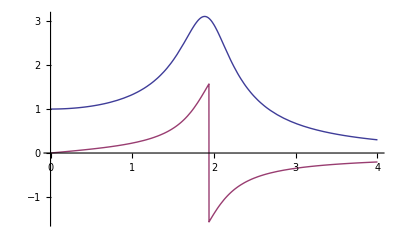

```mathematica
Plot[{Abs [av],ph},{W,0,4}]
```

```mathematica
datar={{0.3084,0.6},{0.4,0.3},{0.5,3*0.2/5},{0.6,2*0.2/5},{0.7,3*0.1/5}}
```

{{0.3084,0.6},{0.4,0.3},{0.5,0.12},{0.6,0.08},{0.7,0.06}}

```mathematica
{{0.3084,0.6},{0.4,0.3},{0.5,0.12000000000000002},{0.6,0.08000000000000002},{0.7,0.06000000000000001}}
LinePlot[datar]
```

{{0.3084,0.6},{0.4,0.3},{0.5,0.12},{0.6,0.08},{0.7,0.06}}

LinePlot[{{0.3084,0.6},{0.4,0.3},{0.5,0.12},{0.6,0.08},{0.7,0.06}}]

```mathematica
LinePlot[{{0.3084,0.6},{0.4,0.3},{0.5,0.12000000000000002},{0.6,0.08000000000000002},{0.7,0.06000000000000001}}]
```

LinePlot[{{0.3084,0.6},{0.4,0.3},{0.5,0.12},{0.6,0.08},{0.7,0.06}}]

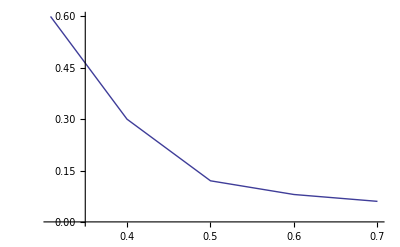

```mathematica
ListLinePlot[{{0.3084,0.6},{0.4,0.3},{0.5,0.12000000000000002},{0.6,0.08000000000000002},{0.7,0.06000000000000001}}]
```

```mathematica
b
```

b

```mathematica
ϕ={0.6,0.3,0.12,0.08,0.06}/0.2;
```

```mathematica
dϕ={0.1,0.2,0.2,0.2,0.02};
```

```mathematica
f={0.308,0.400,0.5,0.6,0.7}
```

{0.308,0.4,0.5,0.6,0.7}

```mathematica
δ={1,0.2,0.1,0.1,0};
```

```mathematica
a=Table[{{2*Pi*f[[i]],ϕ[[i]]},ErrorBar[dϕ[[i]]]},{i,1,5}]
```

{{{1.93522,3.},ErrorBar[0.1]},{{2.51327,1.5},ErrorBar[0.2]},{{3.14159,0.6},ErrorBar[0.2]},{{3.76991,0.4},ErrorBar[0.2]},{{4.39823,0.3},ErrorBar[0.02]}}

```mathematica
b=Table[{{2*Pi*f[[i]],-2*Pi*f[[i]]*δ[[i]]},ErrorBar[0]},{i,1,5}]
```

{{{1.93522,-1.93522},ErrorBar[0]},{{2.51327,-0.502655},ErrorBar[0]},{{3.14159,-0.314159},ErrorBar[0]},{{3.76991,-0.376991},ErrorBar[0]},{{4.39823,0},ErrorBar[0]}}

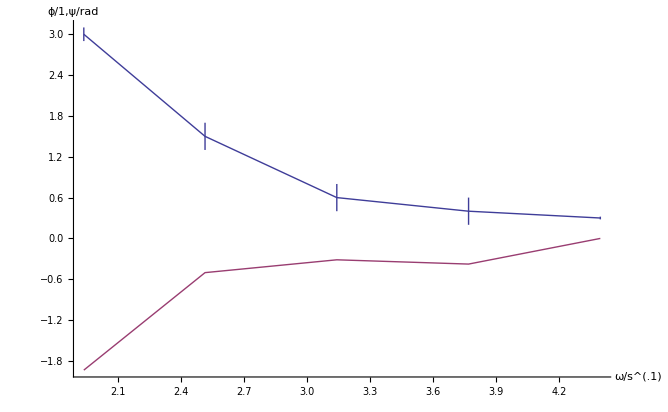

```mathematica
ErrorListPlot[{a,b},Joined->True,AxesLabel->{"ω/s^(.1)","ϕ/1,ψ/rad"},AxesOrigin->{0,0}]
```

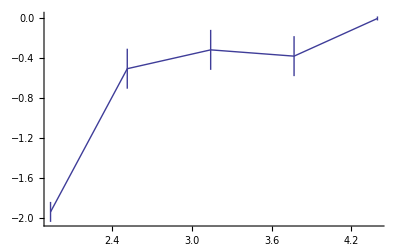

```mathematica
ErrorListPlot[b,Joined->True]
```